## Matrix Product Operators (MPO)

References:
	F. Verstraete, V. Murg, J. I. Cirac
	Matrix product states, projected entangled pair states, and variational renormalization group methods for quantum spin systems
	Advances in Physics 57, 143-224 (2008) DOI

	Thomas Barthel
	Precise evaluation of thermal response functions by optimized density matrix renormalization group schemes
	New Journal of Physics 15, 073010 (2013) DOI

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<mps_base.m
```

```mathematica
(* Pauli matrices *)
Subscript[σ, 1]={{0,1},{1,0}};
Subscript[σ, 2]={{0,-ⅈ},{ⅈ,0}};
Subscript[σ, 3]={{1,0},{0,-1}};
```

### Construct full Hamiltonian as reference

```mathematica
SparseIdentityMatrix[d_]:=SparseArray[{i_,i_}->1,{d,d}]
```

```mathematica
(* construct Ising Hamiltonian (open boundary conditions) *)
Subscript[H, ising][h_,1]:=-h 1/2 Subscript[σ, 3]
Subscript[H, ising][h_,L_]:=Sum[KroneckerProduct[SparseIdentityMatrix[2^(l-1)],1/2 Subscript[σ, 1],1/2 Subscript[σ, 1],SparseIdentityMatrix[2^(L-l-1)]],{l,1,L-1}]-h Sum[KroneckerProduct[SparseIdentityMatrix[2^(l-1)],1/2 Subscript[σ, 3],SparseIdentityMatrix[2^(L-l)]],{l,1,L}]
```

```mathematica
(* number of lattice sites *)
Subscript[L, val]=5;
```

```mathematica
Dimensions[Subscript[H, ising][1,Subscript[L, val]]]
```

{32,32}

```mathematica
Sort[N[Eigenvalues[Subscript[H, ising][1,Subscript[L, val]]]]]
```

{-2.62597,-2.03108,-1.80333,-1.54417,-1.32264,-1.20844,-1.17669,-0.949282,-0.727749,-0.721533,-0.581796,-0.5,-0.354048,-0.240844,-0.126642,-0.0948915,0.0948915,0.126642,0.240844,0.354048,0.5,0.581796,0.721533,0.727749,0.949282,1.17669,1.20844,1.32264,1.54417,1.80333,2.03108,2.62597}

```mathematica
Subscript[β, val]=3/5;
```

```mathematica
(* example *)
Block[{h=1,L=Subscript[L, val],β=Subscript[β, val]},MatrixExp[-β/2 N[Subscript[H, ising][h,L]]]]//MatrixForm
```

(2.13677 | 0. | 0. | -0.120368 | 0. | 0.00811877 | -0.120393 | 0. | 0. | -0.000551558 | 0.00812056 | 0. | -0.120393 | 0. | 0. | 0.00678217 | 0. | 0.0000374772 | -0.000551558 | 0. | 0.00811877 | 0. | 0. | -0.00045736 | -0.120368 | 0. | 0. | 0.00678054 | 0. | -0.00045736 | 0.00678217 | 0.
0. | 1.58373 | -0.118585 | 0. | 0.00811169 | 0. | 0. | -0.0892391 | -0.000551529 | 0. | 0. | 0.00601924 | 0. | -0.0892327 | 0.00668175 | 0. | 0.0000374771 | 0. | 0. | -0.000408834 | 0. | 0.00601746 | -0.000450589 | 0. | 0. | -0.0892142 | 0.00668012 | 0. | -0.000456962 | 0. | 0. | 0.00502716
0. | -0.118585 | 1.5845 | 0. | -0.118613 | 0. | 0. | 0.00734283 | 0.00811349 | 0. | 0. | -0.000498717 | 0. | 0.00668172 | -0.0892824 | 0. | -0.000551529 | 0. | 0. | 0.0000338879 | 0. | -0.000450586 | 0.00602084 | 0. | 0. | 0.00668012 | -0.0892575 | 0. | 0.00668195 | 0. | 0. | -0.000413649
-0.120368 | 0. | 0. | 1.17459 | 0. | -0.0879208 | 0.00734956 | 0. | 0. | 0.00601401 | -0.000498744 | 0. | 0.00678213 | 0. | 0. | -0.0661854 | 0. | -0.000408813 | 0.000033888 | 0. | -0.000457358 | 0. | 0. | 0.00446327 | 0.00678054 | 0. | 0. | -0.066167 | 0. | 0.00495292 | -0.000414028 | 0.
0. | 0.00811169 | -0.118613 | 0. | 1.5845 | 0. | 0. | -0.0892639 | -0.118613 | 0. | 0. | 0.00668191 | 0. | -0.000498716 | 0.00734446 | 0. | 0.00811169 | 0. | 0. | -0.000456959 | 0. | 0.0000338508 | -0.000498716 | 0. | 0. | -0.000456959 | 0.00668191 | 0. | -0.0892639 | 0. | 0. | 0.00502875
0.00811877 | 0. | 0. | -0.0879208 | 0. | 1.1744 | -0.0879428 | 0. | 0. | -0.0879137 | 0.00658298 | 0. | -0.000498743 | 0. | 0. | 0.00544397 | 0. | 0.00601221 | -0.000450194 | 0. | 0.0000338509 | 0. | 0. | -0.000369666 | -0.000457358 | 0. | 0. | 0.00495289 | 0. | -0.0661605 | 0.00495433 | 0.
-0.120393 | 0. | 0. | 0.00734956 | 0. | -0.0879428 | 1.17516 | 0. | 0. | 0.00658302 | -0.0879635 | 0. | 0.00735118 | 0. | 0. | -0.000451886 | 0. | -0.000450196 | 0.00601559 | 0. | -0.000498743 | 0. | 0. | 0.000030671 | 0.00678213 | 0. | 0. | -0.000414026 | 0. | 0.00495433 | -0.0662038 | 0.
0. | -0.0892391 | 0.00734283 | 0. | -0.0892639 | 0. | 0. | 0.871155 | 0.00668195 | 0. | 0. | -0.0652078 | 0. | 0.00544895 | -0.000451861 | 0. | -0.000456962 | 0. | 0. | 0.00445939 | 0. | -0.000369686 | 0.0000306709 | 0. | 0. | 0.00502713 | -0.000413647 | 0. | 0.00502875 | 0. | 0. | -0.0490772
0. | -0.000551529 | 0.00811349 | 0. | -0.118613 | 0. | 0. | 0.00668195 | 1.5845 | 0. | 0. | -0.0892575 | 0. | 0.00602084 | -0.0892824 | 0. | -0.118585 | 0. | 0. | 0.00668012 | 0. | -0.000450586 | 0.00668172 | 0. | 0. | 0.0000338879 | -0.000498717 | 0. | 0.00734283 | 0. | 0. | -0.000413649
-0.000551558 | 0. | 0. | 0.00601401 | 0. | -0.0879137 | 0.00658302 | 0. | 0. | 1.1744 | -0.0879356 | 0. | 0.00601559 | 0. | 0. | -0.0661789 | 0. | -0.0878929 | 0.00658119 | 0. | -0.000450194 | 0. | 0. | 0.0049527 | 0.000033888 | 0. | 0. | -0.000369666 | 0. | 0.00544235 | -0.000407525 | 0.
0.00812056 | 0. | 0. | -0.000498744 | 0. | 0.00658298 | -0.0879635 | 0. | 0. | -0.0879356 | 1.17497 | 0. | -0.0879635 | 0. | 0. | 0.00544541 | 0. | 0.00658119 | -0.0879356 | 0. | 0.00658298 | 0. | 0. | -0.000407522 | -0.000498744 | 0. | 0. | 0.0000306435 | 0. | -0.000407522 | 0.00544541 | 0.
0. | 0.00601924 | -0.000498717 | 0. | 0.00668191 | 0. | 0. | -0.0652078 | -0.0892575 | 0. | 0. | 0.871007 | 0. | -0.065202 | 0.0054504 | 0. | 0.00668012 | 0. | 0. | -0.0651871 | 0. | 0.00487956 | -0.000407896 | 0. | 0. | -0.000369686 | 0.0000306433 | 0. | -0.000413647 | 0. | 0. | 0.0040367
-0.120393 | 0. | 0. | 0.00678213 | 0. | -0.000498743 | 0.00735118 | 0. | 0. | 0.00601559 | -0.0879635 | 0. | 1.17516 | 0. | 0. | -0.0662038 | 0. | -0.000450196 | 0.00658302 | 0. | -0.0879428 | 0. | 0. | 0.00495433 | 0.00734956 | 0. | 0. | -0.000414026 | 0. | 0.000030671 | -0.000451886 | 0.
0. | -0.0892327 | 0.00668172 | 0. | -0.000498716 | 0. | 0. | 0.00544895 | 0.00602084 | 0. | 0. | -0.065202 | 0. | 0.871007 | -0.065224 | 0. | -0.000450589 | 0. | 0. | 0.00487959 | 0. | -0.0651813 | 0.004881 | 0. | 0. | 0.00544734 | -0.000407896 | 0. | 0.0000306709 | 0. | 0. | -0.000334954
0. | 0.00668175 | -0.0892824 | 0. | 0.00734446 | 0. | 0. | -0.000451861 | -0.0892824 | 0. | 0. | 0.0054504 | 0. | -0.065224 | 0.871578 | 0. | 0.00668175 | 0. | 0. | -0.000407898 | 0. | 0.004881 | -0.065224 | 0. | 0. | -0.000407898 | 0.0054504 | 0. | -0.000451861 | 0. | 0. | 0.000027789
0.00678217 | 0. | 0. | -0.0661854 | 0. | 0.00544397 | -0.000451886 | 0. | 0. | -0.0661789 | 0.00544541 | 0. | -0.0662038 | 0. | 0. | 0.646104 | 0. | 0.00495273 | -0.000407525 | 0. | 0.00495433 | 0. | 0. | -0.0483509 | -0.000414028 | 0. | 0. | 0.0040404 | 0. | -0.000334935 | 0.0000277891 | 0.
0. | 0.0000374771 | -0.000551529 | 0. | 0.00811169 | 0. | 0. | -0.000456962 | -0.118585 | 0. | 0. | 0.00668012 | 0. | -0.000450589 | 0.00668175 | 0. | 1.58373 | 0. | 0. | -0.0892142 | 0. | 0.00601746 | -0.0892327 | 0. | 0. | -0.000408834 | 0.00601924 | 0. | -0.0892391 | 0. | 0. | 0.00502716
0.0000374772 | 0. | 0. | -0.000408813 | 0. | 0.00601221 | -0.000450196 | 0. | 0. | -0.0878929 | 0.00658119 | 0. | -0.000450196 | 0. | 0. | 0.00495273 | 0. | 1.17383 | -0.0878929 | 0. | 0.00601221 | 0. | 0. | -0.0661421 | -0.000408813 | 0. | 0. | 0.00446168 | 0. | -0.0661421 | 0.00495273 | 0.
-0.000551558 | 0. | 0. | 0.000033888 | 0. | -0.000450194 | 0.00601559 | 0. | 0. | 0.00658119 | -0.0879356 | 0. | 0.00658302 | 0. | 0. | -0.000407525 | 0. | -0.0878929 | 1.1744 | 0. | -0.0879137 | 0. | 0. | 0.00544235 | 0.00601401 | 0. | 0. | -0.000369666 | 0. | 0.0049527 | -0.0661789 | 0.
0. | -0.000408834 | 0.0000338879 | 0. | -0.000456959 | 0. | 0. | 0.00445939 | 0.00668012 | 0. | 0. | -0.0651871 | 0. | 0.00487959 | -0.000407898 | 0. | -0.0892142 | 0. | 0. | 0.870585 | 0. | -0.0651651 | 0.00544734 | 0. | 0. | 0.0044578 | -0.000369686 | 0. | 0.00502713 | 0. | 0. | -0.0490587
0.00811877 | 0. | 0. | -0.000457358 | 0. | 0.0000338509 | -0.000498743 | 0. | 0. | -0.000450194 | 0.00658298 | 0. | -0.0879428 | 0. | 0. | 0.00495433 | 0. | 0.00601221 | -0.0879137 | 0. | 1.1744 | 0. | 0. | -0.0661605 | -0.0879208 | 0. | 0. | 0.00495289 | 0. | -0.000369666 | 0.00544397 | 0.
0. | 0.00601746 | -0.000450586 | 0. | 0.0000338508 | 0. | 0. | -0.000369686 | -0.000450586 | 0. | 0. | 0.00487956 | 0. | -0.0651813 | 0.004881 | 0. | 0.00601746 | 0. | 0. | -0.0651651 | 0. | 0.870437 | -0.0651813 | 0. | 0. | -0.0651651 | 0.00487956 | 0. | -0.000369686 | 0. | 0. | 0.00403527
0. | -0.000450589 | 0.00602084 | 0. | -0.000498716 | 0. | 0. | 0.0000306709 | 0.00668172 | 0. | 0. | -0.000407896 | 0. | 0.004881 | -0.065224 | 0. | -0.0892327 | 0. | 0. | 0.00544734 | 0. | -0.0651813 | 0.871007 | 0. | 0. | 0.00487959 | -0.065202 | 0. | 0.00544895 | 0. | 0. | -0.000334954
-0.00045736 | 0. | 0. | 0.00446327 | 0. | -0.000369666 | 0.000030671 | 0. | 0. | 0.0049527 | -0.000407522 | 0. | 0.00495433 | 0. | 0. | -0.0483509 | 0. | -0.0661421 | 0.00544235 | 0. | -0.0661605 | 0. | 0. | 0.645682 | 0.00495292 | 0. | 0. | -0.0483345 | 0. | 0.00403895 | -0.000334935 | 0.
-0.120368 | 0. | 0. | 0.00678054 | 0. | -0.000457358 | 0.00678213 | 0. | 0. | 0.000033888 | -0.000498744 | 0. | 0.00734956 | 0. | 0. | -0.000414028 | 0. | -0.000408813 | 0.00601401 | 0. | -0.0879208 | 0. | 0. | 0.00495292 | 1.17459 | 0. | 0. | -0.066167 | 0. | 0.00446327 | -0.0661854 | 0.
0. | -0.0892142 | 0.00668012 | 0. | -0.000456959 | 0. | 0. | 0.00502713 | 0.0000338879 | 0. | 0. | -0.000369686 | 0. | 0.00544734 | -0.000407898 | 0. | -0.000408834 | 0. | 0. | 0.0044578 | 0. | -0.0651651 | 0.00487959 | 0. | 0. | 0.870585 | -0.0651871 | 0. | 0.00445939 | 0. | 0. | -0.0490587
0. | 0.00668012 | -0.0892575 | 0. | 0.00668191 | 0. | 0. | -0.000413647 | -0.000498717 | 0. | 0. | 0.0000306433 | 0. | -0.000407896 | 0.0054504 | 0. | 0.00601924 | 0. | 0. | -0.000369686 | 0. | 0.00487956 | -0.065202 | 0. | 0. | -0.0651871 | 0.871007 | 0. | -0.0652078 | 0. | 0. | 0.0040367
0.00678054 | 0. | 0. | -0.066167 | 0. | 0.00495289 | -0.000414026 | 0. | 0. | -0.000369666 | 0.0000306435 | 0. | -0.000414026 | 0. | 0. | 0.0040404 | 0. | 0.00446168 | -0.000369666 | 0. | 0.00495289 | 0. | 0. | -0.0483345 | -0.066167 | 0. | 0. | 0.645682 | 0. | -0.0483345 | 0.0040404 | 0.
0. | -0.000456962 | 0.00668195 | 0. | -0.0892639 | 0. | 0. | 0.00502875 | 0.00734283 | 0. | 0. | -0.000413647 | 0. | 0.0000306709 | -0.000451861 | 0. | -0.0892391 | 0. | 0. | 0.00502713 | 0. | -0.000369686 | 0.00544895 | 0. | 0. | 0.00445939 | -0.0652078 | 0. | 0.871155 | 0. | 0. | -0.0490772
-0.00045736 | 0. | 0. | 0.00495292 | 0. | -0.0661605 | 0.00495433 | 0. | 0. | 0.00544235 | -0.000407522 | 0. | 0.000030671 | 0. | 0. | -0.000334935 | 0. | -0.0661421 | 0.0049527 | 0. | -0.000369666 | 0. | 0. | 0.00403895 | 0.00446327 | 0. | 0. | -0.0483345 | 0. | 0.645682 | -0.0483509 | 0.
0.00678217 | 0. | 0. | -0.000414028 | 0. | 0.00495433 | -0.0662038 | 0. | 0. | -0.000407525 | 0.00544541 | 0. | -0.000451886 | 0. | 0. | 0.0000277891 | 0. | 0.00495273 | -0.0661789 | 0. | 0.00544397 | 0. | 0. | -0.000334935 | -0.0661854 | 0. | 0. | 0.0040404 | 0. | -0.0483509 | 0.646104 | 0.
0. | 0.00502716 | -0.000413649 | 0. | 0.00502875 | 0. | 0. | -0.0490772 | -0.000413649 | 0. | 0. | 0.0040367 | 0. | -0.000334954 | 0.000027789 | 0. | 0.00502716 | 0. | 0. | -0.0490587 | 0. | 0.00403527 | -0.000334954 | 0. | 0. | -0.0490587 | 0.0040367 | 0. | -0.0490772 | 0. | 0. | 0.47896)

```mathematica
Subscript[A, op][n_,L_]:=KroneckerProduct[SparseIdentityMatrix[2^(Floor[L/2]+n)],1/2 Subscript[σ, 3],SparseIdentityMatrix[2^(L-Floor[L/2]-1-n)]]
```

```mathematica
Dimensions[Subscript[A, op][0,Subscript[L, val]]]
```

{32,32}

```mathematica
(* example *)
Subscript[A, op][1,3]//MatrixForm
```

(1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2)

```mathematica
Z[H_,β_]:=Norm[MatrixExp[-β/2 H],"Frobenius"]^2
```

```mathematica
(* example *)
Block[{h=1,L=Subscript[L, val],β=Subscript[β, val]},Z[N[Subscript[H, ising][h,L]],β]]
```

41.6683

```mathematica
Zref[H_,β_]:=Tr[MatrixExp[-β H]]
```

```mathematica
(* check *)
Block[{h=1,L=Subscript[L, val],β=Subscript[β, val]},Abs[Z[N[Subscript[H, ising][h,L]],β]-Zref[N[Subscript[H, ising][h,L]],β]]]
```

7.10543×10^-15

```mathematica
(* Eq (9) in paper by Barthel, scheme A *)
χA[A_,B_,H_,β_,t_]:=1/Z[H,β] Tr[(MatrixExp[-β/2 H].MatrixExp[ⅈ t H]).B.(MatrixExp[-ⅈ t H].A.MatrixExp[-β/2 H])]
```

```mathematica
(* example *)
Block[{h=1,L=Subscript[L, val],β=Subscript[β, val],t=7},χA[N[Subscript[A, op][0,L]],N[Subscript[A, op][2,L]],N[Subscript[H, ising][h,L]],β,t]]
```

0.110276+0.00159522 ⅈ

```mathematica
(* alternative formulation corresponding to scheme C, see Eq (20) *)
χC[A_,B_,H_,β_,t_]:=Module[{tA=t/2,tB=t/2},1/Z[H,β] Tr[(MatrixExp[ⅈ tB H].MatrixExp[-β/2 H].B.MatrixExp[-ⅈ tB H]).(MatrixExp[-ⅈ tA H].A.MatrixExp[-β/2 H].MatrixExp[ⅈ tA H])]]
```

```mathematica
(* compare *)
Block[{h=1,L=Subscript[L, val],β=Subscript[β, val],t=7},Abs[χC[N[Subscript[A, op][0,L]],N[Subscript[A, op][2,L]],N[Subscript[H, ising][h,L]],β,t]-χA[N[Subscript[A, op][0,L]],N[Subscript[A, op][2,L]],N[Subscript[H, ising][h,L]],β,t]]]
```

2.79211×10^-17

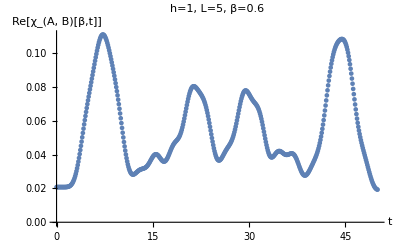

```mathematica
Block[{h=1,L=Subscript[L, val],β=Subscript[β, val]},ListPlot[Re[Table[{t,χA[N[Subscript[A, op][0,L]],N[Subscript[A, op][2,L]],N[Subscript[H, ising][h,L]],β,t]},{t,0,50,0.1}]],AxesLabel->{"t","Re[χ_(A, B)[β,t]]"},PlotLabel->"h="<>ToString[h]<>", L="<>ToString[L]<>", β="<>ToString[N[β]]]]
```

### MPO operations

```mathematica
(* local Hamiltonian terms acting on neighboring lattice sites *)
h2[h_,L_]:=Module[{SzI=KroneckerProduct[1/2 Subscript[σ, 3],IdentityMatrix[2]],ISz=KroneckerProduct[IdentityMatrix[2],1/2 Subscript[σ, 3]]},Table[KroneckerProduct[1/2 Subscript[σ, 1],1/2 Subscript[σ, 1]]-h If[j==1,SzI+1/2 ISz,If[j<L-1,1/2(SzI+ISz),1/2 SzI+ISz]],{j,L-1}]]
```

```mathematica
(* check *)
Block[{L=Subscript[L, val]},Norm[Sum[KroneckerProduct[SparseIdentityMatrix[2^(l-1)],h2[h,L]⟦l⟧,SparseIdentityMatrix[2^(L-l-1)]],{l,1,L-1}]-Subscript[H, ising][h,L]]]
```

0

```mathematica
(* example *)
MatrixForm/@h2[h,Subscript[L, val]]
```

{(-(3 h)/4 | 0 | 0 | 1/4
0 | -h/4 | 1/4 | 0
0 | 1/4 | h/4 | 0
1/4 | 0 | 0 | (3 h)/4),(-h/2 | 0 | 0 | 1/4
0 | 0 | 1/4 | 0
0 | 1/4 | 0 | 0
1/4 | 0 | 0 | h/2),(-h/2 | 0 | 0 | 1/4
0 | 0 | 1/4 | 0
0 | 1/4 | 0 | 0
1/4 | 0 | 0 | h/2),(-(3 h)/4 | 0 | 0 | 1/4
0 | h/4 | 1/4 | 0
0 | 1/4 | -h/4 | 0
1/4 | 0 | 0 | (3 h)/4)}

```mathematica
(* MPO representing identity operation *)
IdMPO[L_]:=Table[ArrayReshape[IdentityMatrix[2],{2,2,1,1}],{i,L}]
```

```mathematica
(* example *)
IdMPO[Subscript[L, val]]
Dimensions[%]
```

{{{{{1}},{{0}}},{{{0}},{{1}}}},{{{{1}},{{0}}},{{{0}},{{1}}}},{{{{1}},{{0}}},{{{0}},{{1}}}},{{{{1}},{{0}}},{{{0}},{{1}}}},{{{{1}},{{0}}},{{{0}},{{1}}}}}

{5,2,2,1,1}

```mathematica
(* check *)
Block[{L=Subscript[L, val]},Norm[MPOMergeFull[IdMPO[L]]-IdentityMatrix[2^L]]]
```

0

#### ⅇ^(-β H/2) MPO approximation

```mathematica
(* example *)
Block[{h=1,L=Subscript[L, val],β=Subscript[β, val],nsteps=20,tol=10^-15},MPOStrangStep[IdMPO[L],N[h2[h,L]],β/2 1/nsteps,tol]]
Dimensions/@%
```

{{{{{4.03122,0.,0.}},{{0.,0.0150036,3.34056×10^-7}}},{{{8.38313×10^-21,0.0150036,-3.34056×10^-7}},{{3.9712,0.,0.}}}},{{{{-0.712385,1.84578×10^-26,1.51728×10^-26},{4.00242×10^-19,-0.00265645,-1.10898×10^-10},{7.45776×10^-17,-0.000140602,-4.97929×10^-6}},{{-1.39137×10^-21,0.00265137,2.9627×10^-8},{0.707102,2.12829×10^-16,4.12983×10^-17},{0.707107,3.5846×10^-14,6.9557×10^-15}}},{{{-1.38616×10^-21,0.00265137,-2.94056×10^-8},{0.707102,-2.12458×10^-21,-3.02878×10^-22},{-0.707107,-3.57965×10^-19,-5.09631×10^-20}},{{-0.701779,4.19912×10^-22,2.1972×10^-24},{3.94986×10^-19,-0.00264651,-1.10483×10^-10},{5.97229×10^-17,0.000138509,4.96375×10^-6}}}},{{{{-0.712385,3.40099×10^-22,-2.81702×10^-27},{6.50179×10^-17,0.00265645,-1.10691×10^-10},{-6.87523×10^-17,0.000140603,-4.97929×10^-6}},{{6.20773×10^-26,0.00265137,-2.9627×10^-8},{-0.707102,-1.97564×10^-16,-4.31578×10^-22},{-0.707107,-3.32986×10^-14,-2.0212×10^-19}}},{{{6.2077×10^-26,0.00265137,2.94056×10^-8},{-0.707102,2.01376×10^-20,-8.62512×10^-22},{0.707107,-1.73151×10^-17,1.34613×10^-19}},{{-0.701779,1.29592×10^-21,-1.50181×10^-26},{-6.67468×10^-17,0.00264651,-1.10691×10^-10},{-5.60785×10^-17,-0.00013851,4.96375×10^-6}}}},{{{{-0.712385,-5.86494×10^-19},{-4.1072×10^-19,0.00265644},{-2.72719×10^-17,-0.000140602}},{{0.,0.00265135},{-0.707102,5.91298×10^-19},{0.707107,-9.25639×10^-15}}},{{{0.,0.00265135},{-0.707102,2.81295×10^-19},{-0.707107,-5.10568×10^-15}},{{-0.701779,5.9091×10^-19},{4.20232×10^-19,0.00264649},{-2.65762×10^-17,0.000138508}}}},{{{{-0.71239},{0.}},{{0.},{-0.707107}}},{{{0.},{-0.707107}},{{-0.701784},{0.}}}}}

{{2,2,1,3},{2,2,3,3},{2,2,3,3},{2,2,3,2},{2,2,2,1}}

```mathematica
(* example *)
Block[{h=1,L=Subscript[L, val],β=Subscript[β, val],nsteps=20,tol=10^-15},MPOSRKNb6Step[IdMPO[L],N[h2[h,L]],β/2 1/nsteps,tol]]
Dimensions/@%
```

{{{{{-1.0086,0.,0.}},{{0.,-0.0613028,-0.000249037}}},{{{-6.59746×10^-19,-0.0613028,0.000249037}},{{-0.993584,0.,0.}}}},{{{{-1.00671,-3.333×10^-16,-1.29998×10^-16},{1.68608×10^-18,-0.00375635,7.4635×10^-7},{3.91904×10^-17,-1.37023×10^-6,-0.0000113055}},{{5.18969×10^-20,0.0611882,0.000285877},{0.0611882,-3.14098×10^-18,-1.30914×10^-16},{0.000248776,9.12135×10^-18,-1.18451×10^-16}}},{{{7.37695×10^-20,0.0611882,-0.000285522},{0.0611882,-1.17761×10^-18,-1.00328×10^-16},{-0.000248777,-1.46204×10^-17,-1.60098×10^-16}},{{-0.991726,3.40041×10^-16,1.17559×10^-16},{-1.99841×10^-18,-0.00373762,-7.56805×10^-7},{-4.01063×10^-17,1.34992×10^-6,0.0000112784}}}},{{{{1.00692,-6.52534×10^-17,5.32968×10^-17},{0.,0.00375712,-1.24409×10^-6},{1.42009×10^-17,-7.4637×10^-7,-0.0000116156}},{{1.5068×10^-19,0.0612006,-0.000254461},{0.0612006,-8.19822×10^-18,3.34622×10^-17},{0.000285924,-1.68715×10^-17,3.88854×10^-17}}},{{{1.33661×10^-19,0.0612006,0.000254462},{0.0612006,-5.40688×10^-18,5.72909×10^-18},{-0.000285569,-8.59244×10^-19,-8.38151×10^-18}},{{0.991927,6.61491×10^-17,-5.65365×10^-17},{8.28832×10^-19,0.00373838,1.22564×10^-6},{-1.3294×10^-17,7.56832×10^-7,0.0000115871}}}},{{{{-1.00692,2.4155×10^-16,-1.54196×10^-16},{6.44302×10^-18,-0.00375711,-2.56265×10^-6},{-4.79297×10^-17,1.24405×10^-6,8.61852×10^-6}},{{2.26724×10^-20,0.0612005,0.000204107},{0.0612006,-2.68718×10^-18,1.73334×10^-18},{-0.000254579,-1.18512×10^-17,-1.71238×10^-17}}},{{{9.72206×10^-21,0.0612005,-0.000203857},{0.0612006,-3.03745×10^-18,-5.23812×10^-18},{0.000254582,-1.64005×10^-16,-8.00731×10^-17}},{{-0.991927,-2.45278×10^-16,1.56098×10^-16},{-6.87988×10^-18,-0.00373837,2.50932×10^-6},{3.78149×10^-17,-1.22566×10^-6,-8.59336×10^-6}}}},{{{{-1.00852},{1.81896×10^-18},{1.36798×10^-17}},{{-3.00794×10^-18},{-0.0612981},{-0.000204123}}},{{{-2.99807×10^-18},{-0.0612981},{0.000204123}},{{-0.993506},{-1.47588×10^-18},{-1.38865×10^-17}}}}}

{{2,2,1,3},{2,2,3,3},{2,2,3,3},{2,2,3,3},{2,2,3,1}}

```mathematica
(* compare *)
Block[{h=1,L=Subscript[L, val],β=Subscript[β, val],nsteps=40,tol=10^-15},Norm[MPOMergeFull[MPOStrangStep[IdMPO[L],N[h2[h,L]],β/2 1/nsteps,tol]]-MatrixExp[-β/2 1/nsteps N[Subscript[H, ising][h,L]]]]]
```

3.68081×10^-8

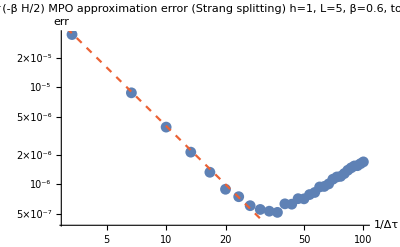

```mathematica
Block[{h=1,L=Subscript[L, val],β=Subscript[β, val],tol=10^-12},Show[ListLogLogPlot[Table[{nsteps/(β/2),1/Z[N[Subscript[H, ising][h,L]],β] Norm[MPOMergeFull[MPOEvolution[MPOStrangStep,IdMPO[L],N[h2[h,L]],β/2,nsteps,tol]]-MatrixExp[-β/2 N[Subscript[H, ising][h,L]]]]},{nsteps,1,30}],AxesLabel->{"1/Δτ","err"},PlotLabel->"ⅇ^(-β H/2) MPO approximation error (Strang splitting)\nh="<>ToString[h]<>", L="<>ToString[L]<>", β="<>ToString[N[β]]<>", tol=10^-12",PlotRange->All],LogLogPlot[0.0004 invΔβ^-2,{invΔβ,1,30},PlotStyle->{ColorData[97][4],Dashed}]]]
```

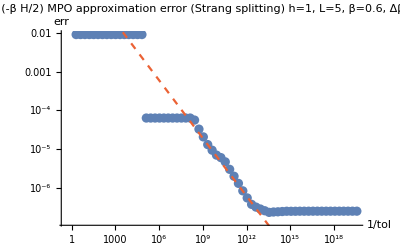

```mathematica
Block[{h=1,L=Subscript[L, val],β=Subscript[β, val],nsteps=12,tol},Show[ListLogLogPlot[Table[tol=2^-i;{1/tol,1/Z[N[Subscript[H, ising][h,L]],β] Norm[MPOMergeFull[MPOEvolution[MPOStrangStep,IdMPO[L],N[h2[h,L]],β/2,nsteps,tol]]-MatrixExp[-β/2 N[Subscript[H, ising][h,L]]]]},{i,1,65}],AxesLabel->{"1/tol","err"},PlotLabel->"ⅇ^(-β H/2) MPO approximation error (Strang splitting)\nh="<>ToString[h]<>", L="<>ToString[L]<>", β="<>ToString[N[β]]<>", Δβ="<>ToString[N[β/nsteps]]],LogLogPlot[0.6 invtol^(-1/2),{invtol,1,2^65},PlotStyle->{ColorData[97][4],Dashed}]]]
```

#### ⅇ^(-ⅈ t H) MPO approximation

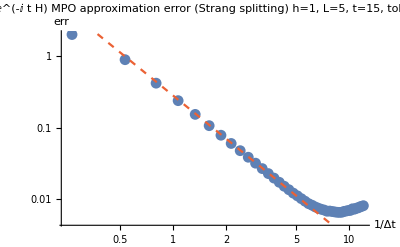

```mathematica
Block[{h=1,L=Subscript[L, val],t=15,tol=10^-8},Show[ListLogLogPlot[Table[{nsteps/t,Norm[MPOMergeFull[MPOEvolution[MPOStrangStep,IdMPO[L],N[h2[h,L]],ⅈ t,nsteps,tol]]-MatrixExp[-ⅈ t N[Subscript[H, ising][h,L]]]]},{nsteps,4,180,4}],AxesLabel->{"1/Δt","err"},PlotLabel->"ⅇ^(-ⅈ t H) MPO approximation error (Strang splitting)\nh="<>ToString[h]<>", L="<>ToString[L]<>", t="<>ToString[t]<>", tol=10^-8",PlotRange->All],LogLogPlot[0.28 invΔt^-2,{invΔt,1/10,20},PlotStyle->{ColorData[97][4],Dashed},PlotRange->All]]]
```

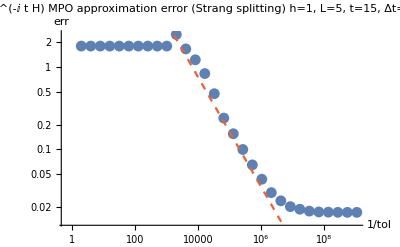

```mathematica
Block[{h=1,L=Subscript[L, val],t=15,Δt=1/4,tol},Show[ListLogLogPlot[Table[tol=2^-i;{1/tol,Norm[MPOMergeFull[MPOEvolution[MPOStrangStep,IdMPO[L],N[h2[h,L]],ⅈ t,t/Δt,tol]]-MatrixExp[-ⅈ t N[Subscript[H, ising][h,L]]]]},{i,1,30}],AxesLabel->{"1/tol","err"},PlotLabel->"ⅇ^(-ⅈ t H) MPO approximation error (Strang splitting)\nh="<>ToString[h]<>", L="<>ToString[L]<>", t="<>ToString[t]<>", Δt="<>ToString[N[Δt]]],LogLogPlot[350 invtol^(-2/3),{invtol,1,2^30},PlotStyle->{ColorData[97][4],Dashed}]]]
```

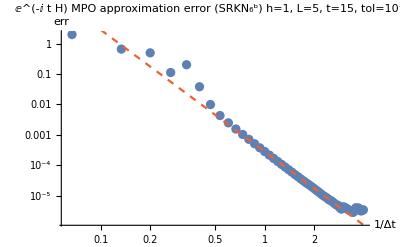

```mathematica
(* can reach smaller errors compared to Strang splitting *)
Block[{h=1,L=Subscript[L, val],t=15,tol=10^-12},Show[ListLogLogPlot[Table[{nsteps/t,Norm[MPOMergeFull[MPOEvolution[MPOSRKNb6Step,IdMPO[L],N[h2[h,L]],ⅈ t,nsteps,tol]]-MatrixExp[-ⅈ t N[Subscript[H, ising][h,L]]]]},{nsteps,1,60}],AxesLabel->{"1/Δt","err"},PlotLabel->"ⅇ^(-ⅈ t H) MPO approximation error (SRKN_6^b)\nh="<>ToString[h]<>", L="<>ToString[L]<>", t="<>ToString[t]<>", tol=10^-12",PlotRange->All],LogLogPlot[0.00028 invΔt^-4,{invΔt,1/10,10},PlotStyle->{ColorData[97][4],Dashed}]]]
```

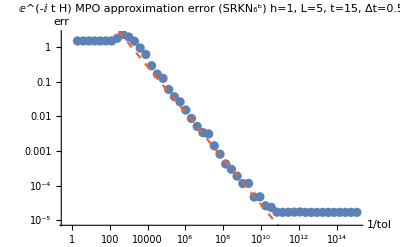

```mathematica
Block[{h=1,L=Subscript[L, val],t=15,Δt=1/2,tol},Show[ListLogLogPlot[Table[tol=2^-i;{1/tol,Norm[MPOMergeFull[MPOEvolution[MPOSRKNb6Step,IdMPO[L],N[h2[h,L]],ⅈ t,t/Δt,tol]]-MatrixExp[-ⅈ t N[Subscript[H, ising][h,L]]]]},{i,1,50}],AxesLabel->{"1/tol","err"},PlotLabel->"ⅇ^(-ⅈ t H) MPO approximation error (SRKN_6^b)\nh="<>ToString[h]<>", L="<>ToString[L]<>", t="<>ToString[t]<>", Δt="<>ToString[N[Δt]]],LogLogPlot[128 invtol^(-2/3),{invtol,1,2^50},PlotStyle->{ColorData[97][4],Dashed}]]]
```

#### ⅇ^(-ⅈ t H)X ⅇ^(ⅈ t H) MPO approximation

```mathematica
SeedRandom[42];
Subscript[A, rnd]=Block[{L=Subscript[L, val],d=2,D=5,zmax},zmax=√2(1+ⅈ)/D;Table[If[j==1,RandomComplex[{-zmax,zmax},{d,d,1,D}],If[j<L,RandomComplex[{-zmax,zmax},{d,d,D,D}],RandomComplex[{-zmax,zmax},{d,d,D,1}]]],{j,L}]];
Dimensions[%]
```

{5,2,2}

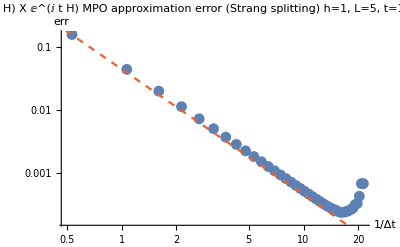

```mathematica
Block[{h=1,L=Subscript[L, val],t=15,tol=10^-8},Show[ListLogLogPlot[Table[{nsteps/t,Norm[MPOMergeFull[MPOEvolution[MPOStrangLiouvilleStep,Subscript[A, rnd],N[h2[h,L]],ⅈ t,nsteps,tol]]-MatrixExp[-ⅈ t N[Subscript[H, ising][h,L]]].MPOMergeFull[Subscript[A, rnd]].MatrixExp[ⅈ t N[Subscript[H, ising][h,L]]]]},{nsteps,8,320,8}],AxesLabel->{"1/Δt","err"},PlotLabel->"ⅇ^(-ⅈ t H) X ⅇ^(ⅈ t H) MPO approximation error (Strang splitting)\nh="<>ToString[h]<>", L="<>ToString[L]<>", t="<>ToString[t]<>", tol=10^-8",PlotRange->All],LogLogPlot[0.045 invΔt^-2,{invΔt,1/10,25},PlotStyle->{ColorData[97][4],Dashed},PlotRange->All]]]
```

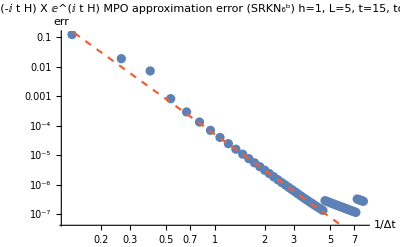

```mathematica
(* can reach smaller errors compared to Strang splitting *)
Block[{h=1,L=Subscript[L, val],t=15,tol=10^-12},Show[ListLogLogPlot[Table[{nsteps/t,Norm[MPOMergeFull[MPOEvolution[MPOSRKNb6LiouvilleStep,Subscript[A, rnd],N[h2[h,L]],ⅈ t,nsteps,tol]]-MatrixExp[-ⅈ t N[Subscript[H, ising][h,L]]].MPOMergeFull[Subscript[A, rnd]].MatrixExp[ⅈ t N[Subscript[H, ising][h,L]]]]},{nsteps,2,120,2}],AxesLabel->{"1/Δt","err"},PlotLabel->"ⅇ^(-ⅈ t H) X ⅇ^(ⅈ t H) MPO approximation error (SRKN_6^b)\nh="<>ToString[h]<>", L="<>ToString[L]<>", t="<>ToString[t]<>", tol=10^-12",PlotRange->All],LogLogPlot[0.00005 invΔt^-4,{invΔt,1/10,10},PlotStyle->{ColorData[97][4],Dashed}]]]
```

#### Response function using MPO approximation

```mathematica
(* example *)
Block[{L=Subscript[L, val],β=Subscript[β, val],t=7},χA[N[Subscript[A, op][0,L]],N[Subscript[A, op][2,L]],N[Subscript[H, ising][1,L]],β,t]]
```

0.110276+0.00159522 ⅈ

```mathematica
(* compare (scheme A) *)
Block[{h=1,L=Subscript[L, val],β=Subscript[β, val],Δβ=Subscript[β, val]/14,ρβ,t=7,Δt=7/16,ρβA,ρβB,tol=10^-13},ρβ=MPOEvolution[MPOStrangStep,IdMPO[L],N[h2[h,L]],1/2 β,β/Δβ,tol];ρβA=MPOEvolution[MPOSRKNb6Step,MPOSingleSiteTopUpdate[ρβ,3,1/2 Subscript[σ, 3]],N[h2[h,L]],ⅈ t,t/Δt,tol];ρβB=MPOEvolution[MPOSRKNb6Step(*MPOStrangStep*),MPOEvolution[MPOSRKNb6Step,MPOSingleSiteTopUpdate[IdMPO[L],5,1/2 Subscript[σ, 3]],N[h2[h,L]],-ⅈ t,t/Δt,tol],N[h2[h,L]],1/2 β,β/Δβ,tol];Abs[MPOFrobeniusNorm[ρβ]^-2 MPOTraceProduct[ρβB,ρβA]-χA[N[Subscript[A, op][0,L]],N[Subscript[A, op][2,L]],N[Subscript[H, ising][1,L]],β,t]]]
```

2.02542×10^-7

```mathematica
(* compare (scheme C) *)
Block[{h=1,L=Subscript[L, val],β=Subscript[β, val],Δβ=Subscript[β, val]/14,ρβ,t=7,tA,tB,Δt=7/16,ρβA,ρβB,tol=10^-13},tA=t/2;tB=t/2;ρβ=MPOEvolution[MPOStrangStep,IdMPO[L],N[h2[h,L]],1/2 β,β/Δβ,tol];ρβA=MPOEvolution[MPOSRKNb6LiouvilleStep,MPOSingleSiteTopUpdate[ρβ,3,1/2 Subscript[σ, 3]],N[h2[h,L]],ⅈ tA,tA/Δt,tol];ρβB=MPOEvolution[MPOSRKNb6LiouvilleStep,MPOSingleSiteBottomUpdate[ρβ,5,1/2 Subscript[σ, 3]],N[h2[h,L]],-ⅈ tB,tB/Δt,tol];{Abs[MPOFrobeniusNorm[ρβ]^-2 MPOTraceProduct[ρβB,ρβA]-χC[N[Subscript[A, op][0,L]],N[Subscript[A, op][2,L]],N[Subscript[H, ising][1,L]],β,t]],Dimensions/@ρβA,Dimensions/@ρβB}]
```

{1.9864×10^-7,{{2,2,1,4},{2,2,4,16},{2,2,16,16},{2,2,16,4},{2,2,4,1}},{{2,2,1,4},{2,2,4,16},{2,2,16,16},{2,2,16,4},{2,2,4,1}}}

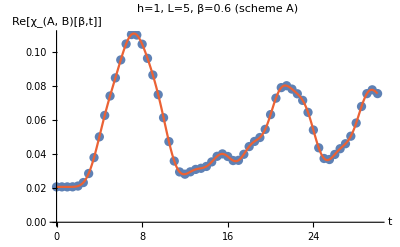

```mathematica
Block[{h=1,L=Subscript[L, val],β=Subscript[β, val],Δβ=Subscript[β, val]/14,ρβ,Δt=1/2,tol=10^-13},ρβ=MPOEvolution[MPOStrangStep,IdMPO[L],N[h2[h,L]],1/2 β,β/Δβ,tol];Show[ListPlot[Re[Table[{n Δt,MPOFrobeniusNorm[ρβ]^-2 MPOTraceProduct[MPOEvolution[MPOSRKNb6Step,MPOEvolution[MPOSRKNb6Step,MPOSingleSiteTopUpdate[IdMPO[L],5,1/2 Subscript[σ, 3]],N[h2[h,L]],-ⅈ n Δt,n,tol],N[h2[h,L]],1/2 β,β/Δβ,tol],MPOEvolution[MPOSRKNb6Step,MPOSingleSiteTopUpdate[ρβ,3,1/2 Subscript[σ, 3]],N[h2[h,L]],ⅈ n Δt,n,tol]]},{n,0,60}]],AxesLabel->{"t","Re[χ_(A, B)[β,t]]"},PlotLabel->"h="<>ToString[h]<>", L="<>ToString[L]<>", β="<>ToString[N[β]]<>" (scheme A)"],ListLinePlot[Re[Table[{t,χA[N[Subscript[A, op][0,L]],N[Subscript[A, op][2,L]],N[Subscript[H, ising][h,L]],β,t]},{t,0,30,0.1}]],PlotStyle->ColorData[97][4]]]]
```

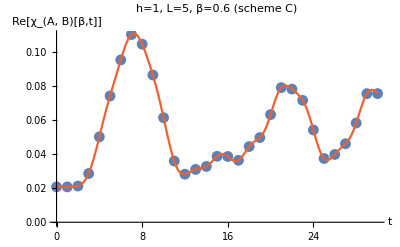

```mathematica
Block[{h=1,L=Subscript[L, val],β=Subscript[β, val],Δβ=Subscript[β, val]/14,ρβ,tA,tB,Δt=1/2,tol=10^-13},ρβ=MPOEvolution[MPOStrangStep,IdMPO[L],N[h2[h,L]],1/2 β,β/Δβ,tol];Show[ListPlot[Re[Table[{n Δt,tA=(n Δt)/2;tB=(n Δt)/2;MPOFrobeniusNorm[ρβ]^-2 MPOTraceProduct[MPOEvolution[MPOSRKNb6LiouvilleStep,MPOSingleSiteBottomUpdate[ρβ,5,1/2 Subscript[σ, 3]],N[h2[h,L]],-ⅈ tB,tB/Δt,tol],MPOEvolution[MPOSRKNb6LiouvilleStep,MPOSingleSiteTopUpdate[ρβ,3,1/2 Subscript[σ, 3]],N[h2[h,L]],ⅈ tA,tA/Δt,tol]]},{n,0,60,2}]],AxesLabel->{"t","Re[χ_(A, B)[β,t]]"},PlotLabel->"h="<>ToString[h]<>", L="<>ToString[L]<>", β="<>ToString[N[β]]<>" (scheme C)"],ListLinePlot[Re[Table[{t,χC[N[Subscript[A, op][0,L]],N[Subscript[A, op][2,L]],N[Subscript[H, ising][h,L]],β,t]},{t,0,30,0.1}]],PlotStyle->ColorData[97][4]]]]
```